# Calculating the Stable, Unstable, and Center Manifolds

In this notebook, we will go over the basic steps of calculating the stable and unstable manifolds associated with the following system:

ẋ=x^2 y-x^5
ẏ=x^2-y^

## Preliminary Definitions

To get started, we need to create function definitions of our functions.

```mathematica
f=.
g=.
```

```mathematica
f[x_,y_] =x^2 y - x^5;
g[x_,y_] = x^2-y;
```

## Finding the Eqilibrium Points

In order to determine the stable, unstable, and/or center manifolds, we need to determine (1) the equilibrium points, and (2) whether or not the equilibrium points are hyperbolic.  Using the command

eqPts =  Solve[{f[x,y]==0,g[x,y]==0},{x,y}]

solves the system of equations

0=x^2 y-x^5
0=x^2-y^

giving us the value of the fixed points.

```mathematica
eqPts = Solve[{f[x,y]==0,g[x,y]==0},{x,y}]
```

{{x→0,y→0},{x→1,y→1}}

## Determining the Stability of the Fixed Point

Let’s focus on the equilibrium point (0,0).  Now that we know that (0,0) is an equilibrium point, we can calclate the Jacobian and then use the

./eqPts[[1]]

command in order to substitute the fixed point into the Jacobian.

```mathematica
Df = {{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}/.eqPts[[1]];
Df//MatrixForm
```

(0 | 0
0 | -1)

Now that we have the Jacobian given by (0 | 0
0 | -1), we can now calculate the eigenvalues of the Jacobian through the following command:

```mathematica
Eigensystem[Df]//MatrixForm
```

(-1 | 0
{0,1} | {1,0})

Since there is an eigenvalue with a zero real part, the equilibrium point is non-hyperbolic.  Thus, we can expect both a stable manifold (correspond to λ = -1) and a center manifold (corresponding to λ = 0).  

Note, if we wanted to find the stable manifold, we would need to let x = h(y) since the eigenvector corresponding to λ = -1 is yields a vertical tangent.  However, let’s start with the center manifold, and then find the stable manifold afterwords.

## Finding the Center Manifold

In order to determine the center manifold, we are looking for a function y = h(x) such that

The equilibrium point is on the center manifold.  That is, y^* = h(x^*) →0 = h(0)

The tangent vector to the center manifold at the equilibrium point is the same as the eigenvector corresponding to the eigenvalue λ = 0. In this case, V^c = (1
0) and so h'(x^*) = 0 →h'(0) = 0.

In order to determine h(x), we will use the invariance condition d/dt(y(t)) =d/dt(h(x(t)) along with the flow

ẋ=x^2 y-x^5
ẏ=x^2-y^

to determine constraints on y = h(x). Using the chain rule along with the system of ODEs, we see that

ẏ = h'(x(t))ẋ  → x^2-y = h'(x)(x^2 y - x^5),     y = h(x),  h(0) = 0.

Replacing y = h(x), we find

x^2-h(x) = h'(x)(x^2 h(x) - x^5), h(0) = 0, h'(0) = 0.

Notice that this is just a non-constant coefficient ODE for h(x).  If we could solve the above differential equation for y = h(x), then we could find the center manifold.

Let’s assume that h(x) has a Taylor Series expansion where

h(x) = a_0 +a_1 x + a_2 x^2+ …

Our goal will be to determine the coefficients a_j for j = 1, 2, …  In the next steps, I will show you how you can use mathematica to determine these coefficients allowing you to approximate the stable manifold.

#### Setting up the series expansion

Now, let’s set up the form h(x) = a_0 +a_1 x + a_2 x^2+a_3 x^3+ a_4 x^4+a_5 x^5+𝒪(x^6)

```mathematica
numTerms = 6; 
h[x_] = Sum[Subscript[a, j] x^j,{j,0,numTerms}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6

Now, we want to solve the equation

x^2-h(x) = h'(x)(x^2 h(x) - x^5), h(0) = 0, h'(0) = 0.

by substituting in the power series for h(x).  To do this, let’s look at the left- and right-hand sides of the equation separately.

```mathematica
LHS = x^2-h[x]
RHS = D[h[x],x](x^2 h[x] - x^5)
```

x^2-a_0-x a_1-x^2 a_2-x^3 a_3-x^4 a_4-x^5 a_5-x^6 a_6

(a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4+5 x^4 a_5+6 x^5 a_6) (-x^5+x^2 (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x^6 a_6))

Now that we have defined the separate sides, we can now begin equating the coefficients of various powers of x by using the `CoefficientList` command.  

This command lists out the coefficients of powers of x starting at x^0 and increasing in sequential order up to x^N where N is the degree of the polynomial in x.

```mathematica
LHSCList = CoefficientList[LHS,x]
RHSCList = CoefficientList[RHS,x]
```

{-a_0,-a_1,1-a_2,-a_3,-a_4,-a_5,-a_6}

{0,0,a_0 a_1,a_1^2+2 a_0 a_2,3 a_1 a_2+3 a_0 a_3,-a_1+2 a_2^2+4 a_1 a_3+4 a_0 a_4,-2 a_2+5 a_2 a_3+5 a_1 a_4+5 a_0 a_5,-3 a_3+3 a_3^2+6 a_2 a_4+6 a_1 a_5+6 a_0 a_6,-4 a_4+7 a_3 a_4+7 a_2 a_5+7 a_1 a_6,4 a_4^2-5 a_5+8 a_3 a_5+8 a_2 a_6,9 a_4 a_5-6 a_6+9 a_3 a_6,5 a_5^2+10 a_4 a_6,11 a_5 a_6,6 a_6^2}

So now, we get a series of equations since we have that the left-hand side must equal the right-hand side.  Thus:

x^0:a_0 = 0
x^1:-a_1 = 0                          → a_1 = 0
x^2: 1-a_2=a_0 a_1            → a_2 = 1

Note that a_0 = 0 since we required that h(0) = 0.  That is, that the equilibriuim point is on the center manifold.  Since we also want h'(0) = 0 so that the tangent matches with our eigenvector, we need a_1 = 0.  We can systematically solve for the remaining coefficients using a ‘For’ loop as follows:

```mathematica
rules = {Subscript[a, 0]->0, Subscript[a, 1]->0};
For[nn=3,nn<numTerms+1,nn++,
sols = Solve[((LHSCList[[nn]]-RHSCList[[nn]])/.rules)==0, Subscript[a, nn-1]];
rules = Flatten[{rules,sols}];
]
```

```mathematica
Sum[Subscript[a, n] x^n,{n,0,numTerms - 1}]/.rules
```

x^2-2 x^5

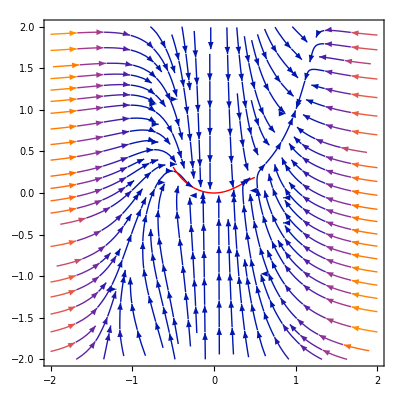

```mathematica
p1 = StreamPlot[{f[x,y],g[x,y]},{x,-2,2},{y,-2,2}];
p2 = Plot[Sum[Subscript[a, n] x^n,{n,0,numTerms-1}]/.rules,{x,-.5,.5},PlotStyle->{Thick,Red}];
Show[p1,p2]
```

```mathematica
numTerms = 10; 
h[x_] = Sum[Subscript[a, j] x^j,{j,0,numTerms}];
LHS = x^2-h[x];
RHS = D[h[x],x](x^2 h[x] - x^5);
LHSCList = CoefficientList[LHS,x];
RHSCList = CoefficientList[RHS,x];
rulesA = {Subscript[a, 0]->0, Subscript[a, 1]->0};
For[nn=3,nn<numTerms+1,nn++,
sols = Solve[((LHSCList[[nn]]-RHSCList[[nn]])/.rulesA)==0, Subscript[a, nn-1]];
rulesA = Flatten[{rulesA,sols}];
]
```

```mathematica
LHS = (x+1)^2-h[x];
RHS = D[h[x],x]((x+1)^2 h[x] - (x+1)^5);
LHSCList = CoefficientList[LHS,x];
RHSCList = CoefficientList[RHS,x];
rulesB = {Subscript[a, 0]->1., Subscript[a, 1]->1.+√3};
For[nn=3,nn<numTerms+1,nn++,
sols = Solve[((LHSCList[[nn]]-RHSCList[[nn]])/.rulesB)==0, Subscript[a, nn-1]];
rulesB = Flatten[{rulesB,sols}];
]
```

```mathematica
LHS = (x+1)^2-h[x];
RHS = D[h[x],x]((x+1)^2 h[x] - (x+1)^5);
LHSCList = CoefficientList[LHS,x];
RHSCList = CoefficientList[RHS,x];
rulesC = {Subscript[a, 0]->1., Subscript[a, 1]->1.-√3};
For[nn=3,nn<numTerms+1,nn++,
sols = Solve[((LHSCList[[nn]]-RHSCList[[nn]])/.rulesC)==0, Subscript[a, nn-1]];
rulesC = Flatten[{rulesC,sols}];
]
```

```mathematica
myRules = {rulesA, rulesB, rulesC}
```

{{a_0→0,a_1→0,a_2→1,a_3→0,a_4→0,a_5→-2,a_6→2,a_7→0,a_8→14,a_9→-26},{a_0→1.,a_1→2.73205,a_2→3.33534,a_3→1.01415,a_4→-1.18942,a_5→4.07408,a_6→-10.2776,a_7→20.0262,a_8→-10.1493,a_9→-240.222},{a_0→1.,a_1→-0.732051,a_2→0.92553,a_3→-1.02077,a_4→1.04762,a_5→-1.03769,a_6→1.01642,a_7→-0.999175,a_8→0.991459,a_9→-0.991924}}

ReplaceAll::reps: {rulesA} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSum::nslim: Limit of summation -1.+numTerms is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

ReplaceAll::reps: {rulesA} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {rulesB} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSum::nslim: Limit of summation -1.+numTerms is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

ReplaceAll::reps: {rulesB} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {rulesC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSum::nslim: Limit of summation -1.+numTerms is not a number.

General::stop: Further output of NSum::nslim will be suppressed during this calculation.

ReplaceAll::reps: {rulesC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

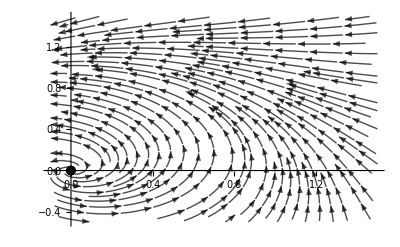

```mathematica
p1 = StreamPlot[{f[x,y],g[x,y]},{x,-.1,1.5},{y,-.5,1.5},
StreamStyle->{Opacity[.7],Black},
StreamColorFunction->None,
StreamPoints->60,
StreamScale->0.1];
p2 = Plot[Sum[Subscript[a, n] x^n,{n,0,numTerms-1}]/.rulesA,{x,-1/2,.45},
PlotStyle->{Thickness[.015],ColorData[97,4],Opacity[.7]}];
p3 = Plot[Sum[Subscript[a, n](x-1)^n,{n,0,numTerms-1}]/.rulesB,{x,.55,1.5},
PlotStyle->{Thickness[.015],ColorData[97,5],Opacity[.7]}];
p4 = Plot[Sum[Subscript[a, n](x-1)^n,{n,0,numTerms-1}]/.rulesC,{x,0,1.5},
PlotStyle->{Thickness[.015],ColorData[97,3],Opacity[.7]}];
p5=ListPlot[{x,y}/.eqPts,
PlotStyle->Black,
PlotMarkers->{Automatic,Medium}];
Show[p2,p3,p4,p1,p5,
PlotRange->{{-.1,1.5},{-.5,1.5}}]
```

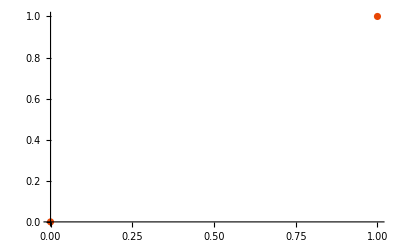

```mathematica
Show[p5]
```

```mathematica
rulesC
```

{a_0→1.,a_1→-0.732051,a_2→0.92553,a_3→-1.02077,a_4→1.04762,a_5→-1.03769,a_6→1.01642,a_7→-0.999175,a_8→0.991459,a_9→-0.991924,a_10→0.996307,a_11→-1.00061,a_12→1.00275,a_13→-1.00258,a_14→1.00117,a_15→-0.999733,a_16→0.999003,a_17→-0.999071,a_18→0.999592,a_19→-1.00013,a_20→1.0004,a_21→-1.00036,a_22→1.00015,a_23→-0.999938,a_24→0.999832,a_25→-0.999851,a_26→0.999941,a_27→-1.00003,a_28→1.00007,a_29→-1.00006}

```mathematica
Plot[Sum[Subscript[a, n](x-1)^n,{n,0,numTerms-1}]/.rulesB,{x,0,1.5},PlotStyle->{Thickness[.01],Orange,Dotted}]
```

-Graphics-